Note: requires CRNSimulator.m to be loaded.

See basic documentation for the key functions:

```mathematica
?SimulateRxnsys
```

SimulateRxnsys[rxnsys,endtime] simulates the reaction system rxnsys for time 0 to endtime. In rxnsys, initial concentrations are specified by conc statements. If no initial condition is set for a species, its initial concentration is set to 0. Rxnsys can also include term[] statements (e.g. term[x, -2 x[t]]) which are additively combined together with term[]s derived from rxn[] statements. Rxnsys can also include direct ODE definitions for some species (e.g. x'[t]==...), or direct definitions of species as functions of time (e.g. x[t]==...), which are passed to NDSolve without modification. Any options specified (eg WorkingPrecision->30) are passed to NDSolve.

```mathematica
?RxnsysToOdesys
```

RxnsysToOdesys[rxnsys,t] returns the ODEs corresponding to reaction system rxnsys, with initial conditions. If no initial condition is set for a species, its initial concentration is set to 0. The time variable is given as the second argument; if omitted it is set to Global`t.

```mathematica
?SpeciesInRxnsys
```

SpeciesInRxnsys[rxnsys] returns the species in reaction system rxnsys. SpeciesInRxnsys[rxnsys,pttrn] returns the species in reaction system rxnsys matching Mathematica pattern pttrn (eg x[1,_]).

### Predator-Prey

```mathematica
rsys={
rxn[x1+x2,2x2,1.5],
rxn[x1,2x1,1],
rxn[x2,1,1],

conc[x1,2],
conc[x2,1]
};
```

```mathematica
tmax=45;
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter={x1[t],x2[t]}/.sol;
```

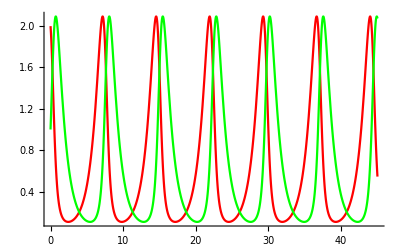

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}}]
```

### Showing: reversible reactions, nanomolar concentrations

```mathematica
rsys={
revrxn[a+b,c,1.5 10^6,10],
rxn[2a,b,10^5],

conc[{a,b,c},10^-9]
};
```

```mathematica
tmax=10*60*60;
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter={a[t],b[t],c[t]}/.sol;
```

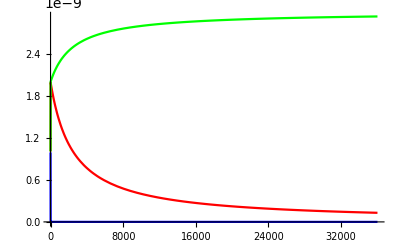

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}}]
```

### Showing: defining modules

In the module definition, Seq[] is used to wrap the reactions and concentrations (rather than { }). This is so that when multiple modules are combined in rsys we won’t get a nested list. Alternatively, Flatten[] could be used to flatten the resulting nested list.

```mathematica
keff=300000;
```

```mathematica
tmax=5*24*60*60;
```

```mathematica
bibi[a_,b_,c_,d_]:=
Module[{gate,backward,agate,out,atrans,helper},
Seq[
revrxn[a+gate,backward+agate,keff/10,keff],
rxn[b+agate,out,keff],
revrxn[out+trans[c], c+atrans,keff/10,keff],
rxn[helper+atrans,d,keff],

conc[{gate,trans[c]}, 200 10^-9],
conc[backward,100 10^-9],
conc[helper, 200 10^-9]

]]
```

```mathematica
rsys=
{bibi[b,a,b,b],
bibi[c,b,c,c],
bibi[a,c,a,a],

conc[b,20 10^-9],
conc[{a,c},5 10^-9]
};
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotSpecies=
Join[
{a,b,c},
{trans[a],trans[b],trans[c]},
SpeciesInRxnsysStringPattern[rsys,"gate$*"]];
```

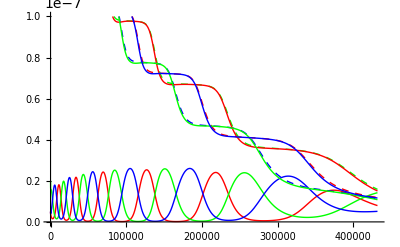

```mathematica
plotter=#[t]/.sol&/@plotSpecies;
Plot[plotter,{t,0,tmax},AxesOrigin->{0,0},PlotRange->{0,100 10^-9},PlotStyle->{{Red,Thick},{Green,Thick},{Blue,Thick},{Red,Thick,Dashed},{Green,Thick,Dashed},{Blue,Thick,Dashed}}]
```

### Example of adding/removing species during experiment

Note: Also requires CRNSimulatorExtensions.m to be loaded

```mathematica
rsys={
revrxn[a+b,c,0.1,30],
rxn[2a,b,0.01],

conc[c,1]
};
```

Don’t specify the initial concentrations of a, b because these are controlled by a schedule. Positive numbers means add this amount, negative numbers means remove this amount. The first column is the time to wait until next addition.

```mathematica
schedule={
{50,4,0},
{20,0,10},
{20,10,0},
{20,0,-9},
{20,-2,0}
};
```

```mathematica
tmax=Total[schedule⟦All,1⟧]
```

130

```mathematica
sol=SimulateRxnsysWithSchedule[rsys,schedule,{a,b}];
```

SimulateRxnsysWithSchedule::undershoot: Scheduled decrease (schedule step 5: -2) resulted in negative concentration. Going to 0.

```mathematica
plotter={a[t],b[t],c[t]}/.sol;
```

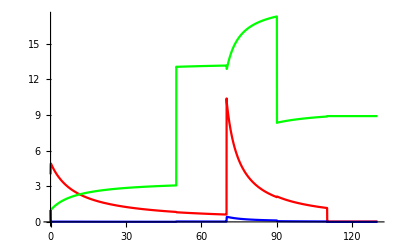

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green},{Blue}}]
```

### Example of non-mass action kinetics: Repressilator

A reaction system can include term[] statements (eg. [x, y[t]/(1+y[t])]), which are additively combined
together to generate the ODEs. You can intermix rxn[] and term[] statements.

```mathematica
tmax=20;
```

```mathematica
n=4;γ=1;β=10;k=5;
```

```mathematica
rsys=
{term[x2,(β k^n)/(k^n+x1[t]^n)],term[x3,(β k^n)/(k^n+x2[t]^n)],term[x1,(β k^n)/(k^n+x3[t]^n)],
term[x1,-γ x1[t]],term[x2,-γ x2[t]],term[x3,-γ x3[t]],

conc[x1,1],conc[x2,0.9],conc[x3,0.1]};
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter={x1[t],x2[t],x3[t]}/.sol;
```

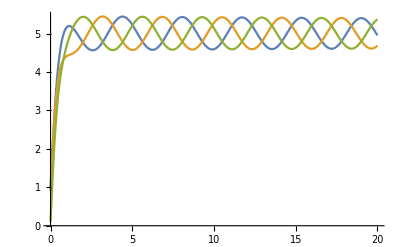

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->All]
```

### Example of providing an external input

You can intermix definitions of the form x[t]==..., x’[t]==..., with rxn, term, and conc statements.

```mathematica
tmax=20;
```

```mathematica
rsys=
{u[t]==0.1 Sin[t]+1,
revrxn[x1+u,x2,1,1],
conc[x1,1]
};
```

```mathematica
sol=SimulateRxnsys[rsys,tmax];
```

```mathematica
plotter={x1[t],x2[t],u[t]}/.sol;
```

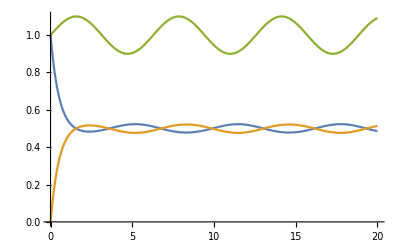

```mathematica
Plot[plotter,{t,0,tmax},PlotRange->All]
```